```mathematica
randomMaze[<|"height"->height_,"width"->width_|>]:=Module[{g,m},g=GridGraph[{height,width}];m=Graph[VertexList[g],Module[{stack={RandomChoice[VertexList[g]]}},
Do[AnnotationValue[{g,v},"Visited"]=False,{v,VertexList[g]}];
AnnotationValue[{g,First@stack},"Visited"]=True;
While[Not[stack=={}],
With[{v=First@stack},
With[{adj=Cases[EdgeList[g,v<->_]/.{v<->u_:>u,u_<->v:>u},x_/;¬AnnotationValue[{g,x},"Visited"]]},
If[adj=={},
stack=Rest@stack,
With[{w=RandomChoice[adj]},
PrependTo[stack,w];
AnnotationValue[{g,w},"Visited"]=True;
Sow[v<->w]]]]]]]//Reap//Last//First, VertexCoordinates->GraphEmbedding[g]](*HighlightGraph[m,PathGraph@FindShortestPath[m,First@VertexList[m],Last@VertexList[m]]]*)]
```

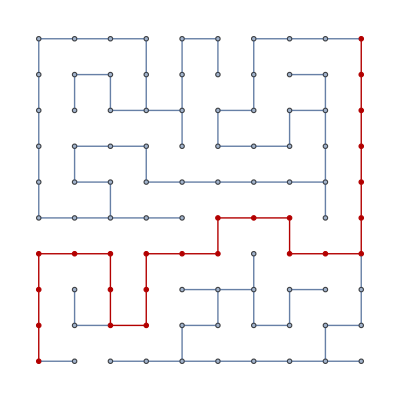

```mathematica
randomMaze[<|"height"->10,"width"->10|>]
```

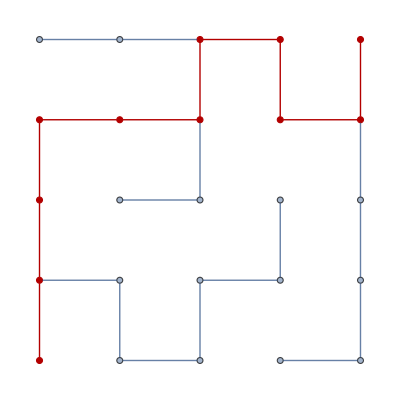

```mathematica
randomMaze[<|"height"->5,"width"->5|>]
```

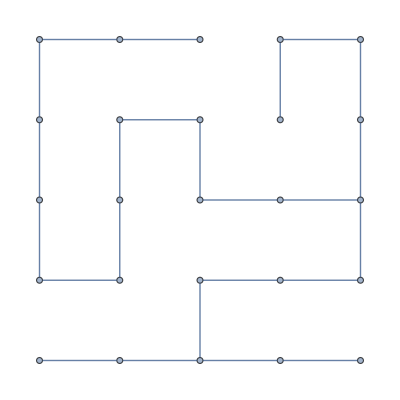

```mathematica
randomMaze[<|"height"->5,"width"->5|>]
```

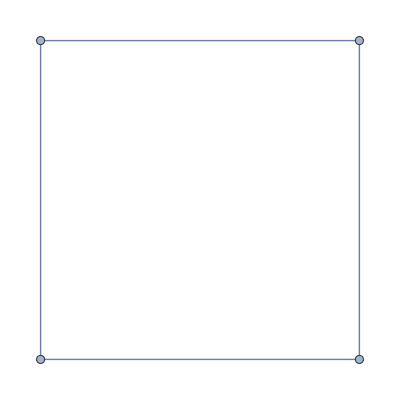

```mathematica
GridGraph[{2,2}]
```

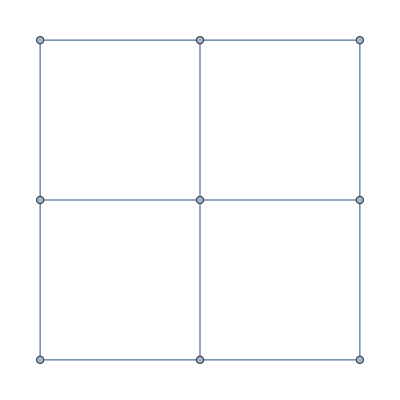

```mathematica
GridGraph[{3,3}]
```

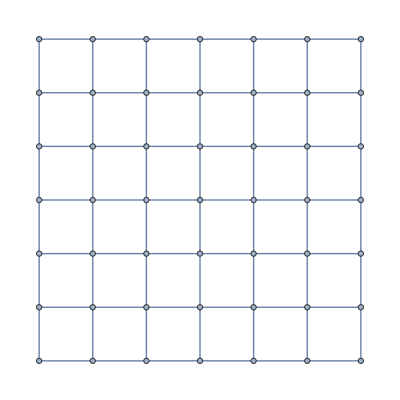

```mathematica
GridGraph[{7,7}]
```

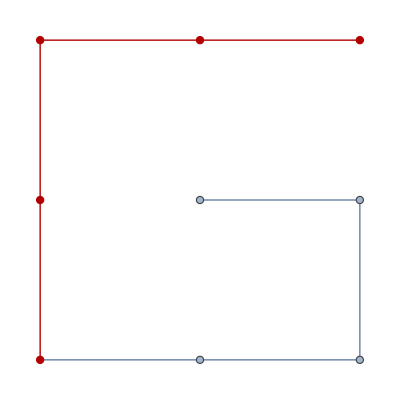

```mathematica
randomMaze[<|"height"->3,"width"->3|>]
```

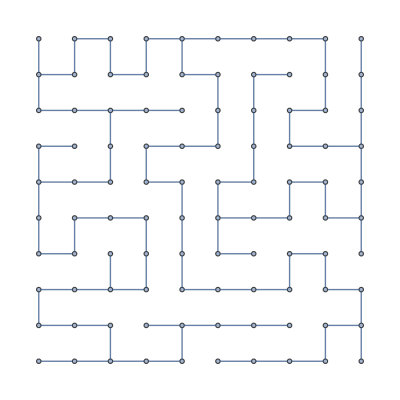

```mathematica
randomMaze[<|"height"->10,"width"->10|>]
```

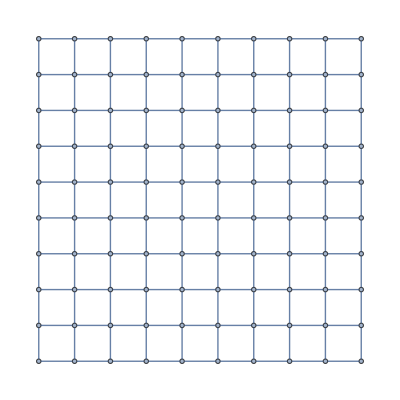

```mathematica
GridGraph[{10,10}]
```

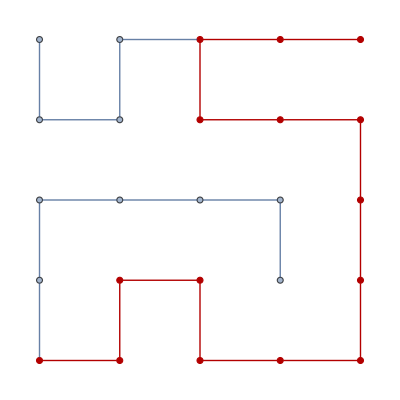

```mathematica
randomMaze[<|"height"->5,"width"->5|>]
```